```mathematica
(*Step 1:Load FeynArts and FeynCalc,and set up the Phi4 model directory*)$LoadAddOns={"FeynArts"};
<<FeynCalc`
modelDir=FileNameJoin[{$FeynCalcDirectory,"Examples","Models","Phi4"}];
{FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]],FileExistsQ[FileNameJoin[{modelDir,"Phi4.gen"}]]}
FAPatch[PatchModelsOnly->True,FAModelsDirectory->modelDir];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

{True,True}

Successfully patched FeynArts.

loading generic model file C:\Users\king\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4.gen

> $GenericMixing is OFF

generic model {C:\Users\king\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4} initialized

loading classes model file C:\Users\king\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

> 2 counterterms of order 1

classes model {C:\Users\king\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4} initialized

in total: 0 Classes insertions

creating amplitudes at level(s) {Classes}

in total: 0 Classes amplitudes

0

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 ac\bc\cc.m, 0 diagrams

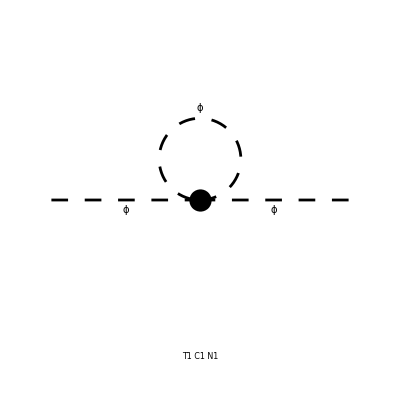

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

{(ⅈ g m^2)/(32 π^2 eps)+(ⅈ g m^2 log(2 π))/(16 π^2)+O(eps^1),(ⅈ g m^2)/(32 π^2 eps)+(ⅈ g m^2 log(2 π))/(16 π^2)+(ⅈ g m^2 log^2(2 π) eps)/(16 π^2)+O(eps^2)}

```mathematica
(*Zeroth-order (tree-level) 1->1 process (or contact) diagram*)treeTadpole=InsertFields[CreateTopologies[0,1->1],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[treeTadpole];

faTreeTad=CreateFeynAmp[treeTadpole,PreFactor->1];
fcTreeTad=FCFAConvert[faTreeTad,IncomingMomenta->{p1},OutgoingMomenta->{k1},List->False];
fcTreeTad

(*First-order (one-loop) tadpole diagram*)
tadpole=InsertFields[CreateTopologies[1,1->1],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[tadpole];

faTad=CreateFeynAmp[tadpole,PreFactor->1];
fcTad=FCFAConvert[faTad,IncomingMomenta->{p1},OutgoingMomenta->{k1},LoopMomenta->{q},ChangeDimension->D,List->False];
tadPV=ToPaVe[fcTad/. mphi->m,q];

uvTad=PaVeUVPart[tadPV,Prefactor->1/(2 Pi)^D];

seriesOrderZero=Series[uvTad/. D->4-2 eps,{eps,0,0}];
seriesOrderOne=Series[uvTad/. D->4-2 eps,{eps,0,1}];

{seriesOrderZero,seriesOrderOne}
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

{True,True}

Successfully patched FeynArts.

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe\cede\0.m, 0 diagrams

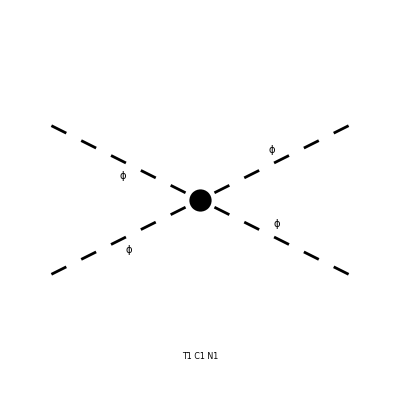

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

-ⅈ g

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 1 Classes insertion

> Top. 17: 1 Classes insertion

> Top. 18: 1 Classes insertion

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

> Top. 26: 0 Classes insertions

> Top. 27: 0 Classes insertions

> Top. 28: 0 Classes insertions

> Top. 29: 0 Classes insertions

> Top. 30: 0 Classes insertions

> Top. 31: 0 Classes insertions

> Top. 32: 0 Classes insertions

> Top. 33: 0 Classes insertions

> Top. 34: 0 Classes insertions

> Top. 35: 0 Classes insertions

> Top. 36: 0 Classes insertions

> Top. 37: 0 Classes insertions

> Top. 38: 0 Classes insertions

> Top. 39: 0 Classes insertions

> Top. 40: 0 Classes insertions

> Top. 41: 0 Classes insertions

> Top. 42: 0 Classes insertions

> Top. 43: 0 Classes insertions

> Top. 44: 0 Classes insertions

> Top. 45: 0 Classes insertions

> Top. 46: 0 Classes insertions

> Top. 47: 0 Classes insertions

> Top. 48: 0 Classes insertions

> Top. 49: 0 Classes insertions

> Top. 50: 0 Classes insertions

> Top. 51: 0 Classes insertions

in total: 3 Classes insertions

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

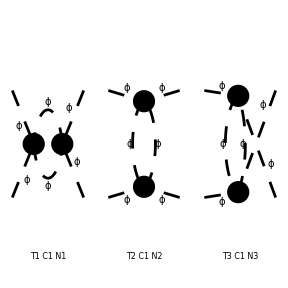

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

{(3 ⅈ g^2)/(32 π^2 eps)+(3 ⅈ g^2 log(2 π))/(16 π^2)+O(eps^1),(3 ⅈ g^2)/(32 π^2 eps)+(3 ⅈ g^2 log(2 π))/(16 π^2)+(3 ⅈ g^2 log^2(2 π) eps)/(16 π^2)+O(eps^2)}

```mathematica
(*Load FeynArts and FeynCalc,and set up the Phi4 model directory*)$LoadAddOns={"FeynArts"};
<<FeynCalc`
modelDir=FileNameJoin[{$FeynCalcDirectory,"Examples","Models","Phi4"}];
{FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]],FileExistsQ[FileNameJoin[{modelDir,"Phi4.gen"}]]}
FAPatch[PatchModelsOnly->True,FAModelsDirectory->modelDir];

(* ===4-POINT FUNCTION:Tree Level (0-loop,2->2 scattering)===*)
tree=InsertFields[CreateTopologies[0,2->2],{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[tree];

faTree=CreateFeynAmp[tree,PreFactor->1];
fcTree=FCFAConvert[faTree,IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False];
fcTree

(* ===4-POINT FUNCTION:One-Loop (Bubbles,excluding wave-function corrections)===*)
bubbles=InsertFields[CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections}],{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[bubbles];

faLoop=CreateFeynAmp[bubbles,PreFactor->1];
fcLoop=FCFAConvert[faLoop,IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},ChangeDimension->D,List->False];

bubblePV=ToPaVe[fcLoop/. mphi->m,q];

uvBubble=PaVeUVPart[bubblePV,Prefactor->1/(2 Pi)^D];

seriesOrderZeroBubble=Series[uvBubble/. D->4-2 eps,{eps,0,0}];
seriesOrderOneBubble=Series[uvBubble/. D->4-2 eps,{eps,0,1}];

{seriesOrderZeroBubble,seriesOrderOneBubble}
```

```mathematica
--------------------------------------------------------
```

1.2) cutoff and Dimensional Regularization

```mathematica
dim=4-2*ϵ;
OmegaD[d_]:=(2*Pi^(d/2))/Gamma[d/2];

(*Radial integral:int_0^Lambda k^(dim-1)/(k^2+m^2) dk*)
rawVal=Integrate[k^(dim-1)/(k^2+m^2),{k,0,Λ},Assumptions->{Λ>0,m^2>0}]/. D->dim;

(*1. Exact T without (2pi)^D prefactor (using solid angle Omega_D)*)
exactT1=OmegaD[dim]*rawVal;
Print["--- 1. Exact T (without (2pi)^D) ---"];
Print[exactT1];

asympT1=Asymptotic[exactT1,{Λ,Infinity,2}];
Print["Expanded in large Lambda:"];
Print[FullSimplify[asympT1]];

(*2. Exact T divided by (2pi)^D (Standard QFT loop measure)*)
exactT2=(1/(2*Pi)^dim)*exactT1;
Print["--- 2. Exact T / (2pi)^D ---"];
Print[exactT2];

asympT2=Asymptotic[exactT2,{Λ,Infinity,2}];
Print["Expanded in large Lambda:"];
Print[FullSimplify[asympT2]];
```

--- 1. Exact T (without (2pi)^D) ---

ConditionalExpression[(m^2 π^(1/2 (4-2 ϵ)) (-1/m^2)^ϵ -Λ^2/m^22-ϵ0)/(1/2 (4-2 ϵ)), Re(ϵ)<2]

Expanded in large Lambda:

ConditionalExpression[(π^(2-ϵ) (ϵ-2) Λ^(-2 ϵ) (Λ^2+π m^2 (ϵ-1) csc(π ϵ) (Λ^2/m^2)^ϵ))/((ϵ-1) 3-ϵ), Re(ϵ)<2]

--- 2. Exact T / (2pi)^D ---

ConditionalExpression[(m^2 2^(2 ϵ-4) π^(1/2 (4-2 ϵ)+2 ϵ-4) (-1/m^2)^ϵ -Λ^2/m^22-ϵ0)/(1/2 (4-2 ϵ)), Re(ϵ)<2]

Expanded in large Lambda:

ConditionalExpression[((4 π)^(ϵ-2) (ϵ-2) Λ^(-2 ϵ) (Λ^2+π m^2 (ϵ-1) csc(π ϵ) (Λ^2/m^2)^ϵ))/((ϵ-1) 3-ϵ), Re(ϵ)<2]

```mathematica
dim=4-2*ϵ;
OmegaD[d_]:=(2*Pi^(d/2))/Gamma[d/2];

(*Define T and B(0)*)
rawValT=Integrate[k^(dim-1)/(k^2+m^2),{k,0,Λ},Assumptions->{Λ>0,m>0}]/. D->dim;
tExpr=(1/(2*Pi)^dim)*OmegaD[dim]*rawValT;

rawValB0=Integrate[k^(dim-1)/(k^2+m^2)^2,{k,0,Λ},Assumptions->{Λ>0,m>0}]/. D->dim;
b0Expr=(1/(2*Pi)^dim)*OmegaD[dim]*rawValB0;

(*Asymptotic expansions in large Lambda*)
asympT=Asymptotic[tExpr,{Λ,Infinity,2}];
asympB0=Asymptotic[b0Expr,{Λ,Infinity,2}];

(*Apply chain rule:-d(T)/d(m^2)=-(1/(2m))*d(T)/dm*)
rhsAsymp=-(1/(2*m))*D[asympT,m];

Print["Asymptotic - d(T)/dm^2:"];
Print[FullSimplify[rhsAsymp]];

Print["\nAsymptotic B(0):"];
Print[FullSimplify[asympB0]];
```

Asymptotic - d(T)/dm^2:

ConditionalExpression[1/(1-ϵ)(-1)^ϵ 4^(ϵ-2) π^(ϵ-1) (-1/m^2)^-ϵ m^(-2 ϵ) Λ^(-2 ϵ) csc(π ϵ) (Λ^2/m^2)^ϵ, Re(ϵ)<2]

Asymptotic B(0):

ConditionalExpression[-1/(16 π^2 (ϵ+1) 2-ϵ)(-1/m^2)^(1-ϵ) Λ^(-4 ϵ-2) (-Λ^2 m^2 4^ϵ π^(ϵ+1) (ϵ^2-1) csc(π ϵ) (-Λ^4/m^4)^ϵ+1/((ϵ-1) ϵ)(m^4 2^(2 ϵ+1) π^ϵ ϵ^2-(4 π)^ϵ (m^4 (ϵ^3+ϵ)-Λ^2 m^2 (ϵ-1)^2 (ϵ+1)+Λ^4 ϵ (ϵ^2-1))) (-Λ^2/m^2)^ϵ+(ϵ+1) (Λ^4+m^4-Λ^2 m^2) ⅇ^(ϵ (2 log(Λ)+log(-(4 π)/m^2)))), Re(ϵ)<2]

```mathematica
Simplify[rhsAsymp==asympB0]
```

ConditionalExpression[(m^(-2 ϵ-1) Λ^(-2 ϵ-1) (-m^(2 ϵ) 1-ϵ 3-ϵ (m^4 ϵ ((4 π)^ϵ (ϵ^2+1)-2^(2 ϵ+1) π^ϵ ϵ)-Λ^2 m^2 (4 π)^ϵ (ϵ-1)^2 (ϵ+1)+Λ^4 (4 π)^ϵ ϵ (ϵ^2-1)) (-Λ^2/m^2)^ϵ-ϵ (2-ϵ)^2 ((2^(2 ϵ+1) π^ϵ-(4 π)^ϵ (ϵ-1) ϵ) (Λ^4+m^4-Λ^2 m^2) (-1/m^2)^ϵ m^(2 ϵ) Λ^(2 ϵ)-Λ^2 m^2 (ϵ^2-1) 3-ϵ ϵ-1 ((-4 π)^ϵ Λ^(2 ϵ) (Λ^2/m^2)^ϵ-(4 π)^ϵ m^(2 ϵ) (-Λ^4/m^4)^ϵ))))/(ϵ (ϵ+1) 2-ϵ)==0, Re(ϵ)<2]

```mathematica
dim=4-2*epsilon;
OmegaD[d_]:=(2*Pi^(d/2))/Gamma[d/2];

(*Define exact T and B(0) expressions*)
rawValT=Integrate[k^(dim-1)/(k^2+m^2),{k,0,Lambda},Assumptions->{Lambda>0,m>0}]/. D->dim;
tExpr=(1/(2*Pi)^dim)*OmegaD[dim]*rawValT;

rawValB0=Integrate[k^(dim-1)/(k^2+m^2)^2,{k,0,Lambda},Assumptions->{Lambda>0,m>0}]/. D->dim;
b0Expr=(1/(2*Pi)^dim)*OmegaD[dim]*rawValB0;

(*1. Series expansion in small epsilon (up to O(epsilon^1))*)
epsT=Series[tExpr,{epsilon,0,1}];
epsB0=Series[b0Expr,{epsilon,0,1}];

(*2. Apply chain rule:-d(T)/d(m^2)=-(1/(2m))*d(T)/dm on epsilon-expanded T*)
rhsEps=-(1/(2*m))*D[Normal[epsT],m];

Print["Epsilon-expanded - d(T)/dm^2:"];
Print[FullSimplify[rhsEps]];

Print["\nEpsilon-expanded B(0):"];
Print[FullSimplify[Normal[epsB0]]];

(*3. Test equality*)
Print["\nAre they equal?"];
Print[Simplify[rhsEps==Normal[epsB0]]];
```

Epsilon-expanded - d(T)/dm^2:

1/(16 π^2)(-epsilon 2-Lambda^2/m^2-epsilon log(Lambda^2/m^2+1)+-Lambda^2/m^220 (epsilon log(-Lambda^2/(4 π m^2))+2 epsilon log(m)+(-1+ℽ-ⅈ π) epsilon-1)+1/(m^2 (Lambda^2+m^2))Lambda^4 (-(epsilon (log(-Lambda^2/(4 π m^2))+2 log(m)))+ⅈ π epsilon-ℽ epsilon+epsilon+1))

Epsilon-expanded B(0):

(-ℽ epsilon Lambda^4+epsilon Lambda^4 (-2 log(Lambda)+log(π)+log(4))-epsilon m^2 (Lambda^2+m^2) 2-Lambda^2/m^2-epsilon Lambda^2 m^2+m^2 (Lambda^2+m^2) (2 epsilon log(Lambda)+ℽ epsilon-epsilon log(4 π)-1) -Lambda^2/m^220+Lambda^4)/(16 π^2 m^2 (Lambda^2+m^2))

Are they equal?

1/(m (Lambda^2+m^2))epsilon (-2 Lambda^4 log(m)+ⅈ π Lambda^4+Lambda^4+2 Lambda^4 log(Lambda)+Lambda^2 m^2-Lambda^2 m^2 log(Lambda^2/m^2+1)+m^2 (Lambda^2+m^2) (log(-Lambda^2/m^2)-2 log(Lambda)+2 log(m)-ⅈ π-1) -Lambda^2/m^220-m^4 log(Lambda^2/m^2+1)-Lambda^4 log(-Lambda^2/m^2))==0

```mathematica
dim=4-2*epsilon;
OmegaD[d_]:=(2*Pi^(d/2))/Gamma[d/2];
measure[d_]:=OmegaD[d]/(2*Pi)^d;

(*---1. Mass Counterterm (delta_m^2)---*)
rawT=Integrate[k^(dim-1)/(k^2+m^2),{k,0,Lambda},Assumptions->{Lambda>0,m^2>0}]/. D->dim;
tCutoff=measure[dim]*rawT;
asympT=Asymptotic[tCutoff,{Lambda,Infinity,2}];
deltaM2=-(lambda/2)*asympT;

Print["=== 1. MASS COUNTERTERM (delta_m^2) ==="];
Print[FullSimplify[deltaM2]];

(*---2. Coupling Counterterm (delta_lambda)---*)
rawB0=Integrate[k^(dim-1)/(k^2+m^2)^2,{k,0,Lambda},Assumptions->{Lambda>0,m^2>0}]/. D->dim;
b0Cutoff=measure[dim]*rawB0;
asympB0=Asymptotic[b0Cutoff,{Lambda,Infinity,2}];
deltaLambda=(3*lambda^2/2)*asympB0;

Print["\n=== 2. COUPLING COUNTERTERM (delta_lambda) ==="];
Print[FullSimplify[deltaLambda]];

(*---3. Convergent Difference B(P^2)-B(0) as Lambda->Infinity---*)
DeltaExpr=m^2+x*(1-x)*P^2;
innerB=(Lambda^dim/(dim*DeltaExpr^2))*Hypergeometric2F1[2,dim/2,(2+dim)/2,-Lambda^2/DeltaExpr];
rawB=Integrate[innerB,{x,0,1},Assumptions->{Lambda>0,m^2>0,P>0,dim>0}]/. D->dim;
bCutoff=measure[dim]*rawB;

bDiff=bCutoff-(bCutoff/. P->0);
asympBDiff=Asymptotic[bDiff,{Lambda,Infinity,2}];

Print["\n=== 3. CONVERGENT DIFFERENCE B(P^2) - B(0) (Lambda -> Infinity) ==="];
Print[FullSimplify[asympBDiff]];
```

=== 1. MASS COUNTERTERM (delta_m^2) ===

ConditionalExpression[(2^(2 epsilon-5) (2-epsilon) π^(epsilon-2) lambda Lambda^(-2 epsilon) (π (epsilon-1) m^2 csc(π epsilon) (Lambda^2/m^2)^epsilon+Lambda^2))/((epsilon-1) 3-epsilon), Re(epsilon)<2]

=== 2. COUPLING COUNTERTERM (delta_lambda) ===

ConditionalExpression[-((3 lambda^2 Lambda^(-4 epsilon-2) (-1/m^2)^(1-epsilon) (((-Lambda^2/m^2)^epsilon (2^(2 epsilon+1) epsilon^2 π^epsilon m^4-(4 π)^epsilon (epsilon (epsilon^2-1) Lambda^4+epsilon (epsilon^2+1) m^4-(epsilon-1)^2 (epsilon+1) Lambda^2 m^2)))/((epsilon-1) epsilon)-4^epsilon (epsilon^2-1) π^(epsilon+1) Lambda^2 m^2 csc(π epsilon) (-Lambda^4/m^4)^epsilon+(epsilon+1) (Lambda^4-Lambda^2 m^2+m^4) ⅇ^(epsilon (2 log(Lambda)+log(-(4 π)/m^2)))))/(32 π^2 (epsilon+1) 2-epsilon)), Re(epsilon)<2]

Integrate::fas: Warning: one or more assumptions evaluated to False.

=== 3. CONVERGENT DIFFERENCE B(P^2) - B(0) (Lambda -> Infinity) ===

-((4^(epsilon-2) (epsilon-2) π^(epsilon-1) Lambda^(-2 epsilon) csc(π epsilon) (Lambda^2/m^2)^epsilon (m^2 (12-2 epsilon2-epsilonP^2/(2 √(P^4+4 m^2 P^2))+1/2-12-2 epsilon2-epsilon1/2-P^2/(2 √(P^4+4 m^2 P^2)))+(epsilon-1) √(4 m^2 P^2+P^4)))/(3-epsilon √(4 m^2 P^2+P^4)))

```mathematica
dim=4-2*epsilon;
OmegaD[d_]:=(2*Pi^(d/2))/Gamma[d/2];
measure[d_]:=OmegaD[d]/(2*Pi)^d;

(*1. Cutoff Regularization Bubble difference (Lambda->Infinity)*)
DeltaExpr=m^2+x*(1-x)*P^2;
innerB=(Lambda^dim/(dim*DeltaExpr^2))*Hypergeometric2F1[2,dim/2,(2+dim)/2,-Lambda^2/DeltaExpr];
rawB=Integrate[innerB,{x,0,1},Assumptions->{Lambda>0,m^2>0,P>0,dim>0}]/. D->dim;
bCutoff=measure[dim]*rawB;
bDiffCutoff=bCutoff-(bCutoff/. P->0);
asympBDiff=Asymptotic[bDiffCutoff,{Lambda,Infinity,2}];

Print["=== Cutoff Regularization B(P^2) - B(0) (Lambda -> Inf) ==="];
Print[FullSimplify[asympBDiff]];

(*2. Dimensional Regularization Bubble difference*)
dimRegDiff=-(1/(16*Pi^2))*Integrate[Log[1+x*(1-x)*P^2/m^2],{x,0,1},Assumptions->{m^2>0,P>0}];
Print["\n=== Dimensional Regularization B(P^2) - B(0) ==="];
Print[FullSimplify[dimRegDiff]];

(*3. Slopes at P^2=0*)
serCutoff=Series[asympBDiff,{P,0,2}];
slopeCutoff=SeriesCoefficient[serCutoff,{P,0,2}];

serDimReg=Series[dimRegDiff,{P,0,2}];
slopeDimReg=SeriesCoefficient[serDimReg,{P,0,2}];

Print["\n=== Slope at P^2 = 0 ==="];
Print["Cutoff slope:  ",FullSimplify[slopeCutoff]];
Print["Dim Reg slope: ",FullSimplify[slopeDimReg]];
```

=== Cutoff Regularization B(P^2) - B(0) (Lambda -> Inf) ===

-((4^(epsilon-2) (epsilon-2) π^(epsilon-1) Lambda^(-2 epsilon) csc(π epsilon) (Lambda^2/m^2)^epsilon (m^2 (12-2 epsilon2-epsilonP^2/(2 √(P^4+4 m^2 P^2))+1/2-12-2 epsilon2-epsilon1/2-P^2/(2 √(P^4+4 m^2 P^2)))+(epsilon-1) √(4 m^2 P^2+P^4)))/(3-epsilon √(4 m^2 P^2+P^4)))

=== Dimensional Regularization B(P^2) - B(0) ===

(P-√(4 m^2+P^2) tanh^-1(P/(√(4 m^2+P^2))))/(8 π^2 P)

=== Slope at P^2 = 0 ===

Cutoff slope:  ((2^(2 epsilon-5) Lambda^(-2 epsilon) (Lambda^2/m^2)^epsilon π^(epsilon-1) csc(epsilon π))/(3 m^2 -epsilon))

Dim Reg slope: -1/(96 m^2 π^2)

```mathematica
(*Mathematica script to derive MS beta function,fixed point,delta_Z,and compare MS vs finite subtraction*)Print["=================================================="];
Print["1. ONE-LOOP FIELD COUNTERTERM (delta_Z)"];
Print["=================================================="];
Print["At one-loop order in phi^4 theory, self-energy Sigma(p^2) is constant. Hence delta_Z = 0."];

Print["\n=================================================="];
Print["2. MINIMAL-SUBTRACTION (MS) BETA FUNCTION THROUGH g^2"];
Print["=================================================="];
beta[g_,epsilon_]:=-epsilon*g+3*g^2;
fixedPoint=Solve[beta[g,epsilon]==0&&g!=0,g][[1]];
Print["Nonzero fixed point g^*: ",fixedPoint];

Print["\n=================================================="];
Print["3. WHY TADPOLE CANNOT CHANGE MOMENTUM EXPONENT"];
Print["=================================================="];
Print["Tadpole diagrams are momentum-independent; they only shift m^2 and cannot generate p^2 dependence."];

Print["\n=================================================="];
Print["4. MS VS FINITE SUBTRACTION"];
Print["=================================================="];
Print["MS removes pure 1/epsilon poles. Finite subtraction absorbs finite logs and constants via physical momentum conditions."];
```

==================================================

1. ONE-LOOP FIELD COUNTERTERM (delta_Z)

==================================================

At one-loop order in phi^4 theory, self-energy Sigma(p^2) is constant. Hence delta_Z = 0.

==================================================

2. MINIMAL-SUBTRACTION (MS) BETA FUNCTION THROUGH g^2

==================================================

Nonzero fixed point g^*: {g→epsilon/3}

==================================================

3. WHY TADPOLE CANNOT CHANGE MOMENTUM EXPONENT

==================================================

Tadpole diagrams are momentum-independent; they only shift m^2 and cannot generate p^2 dependence.

==================================================

4. MS VS FINITE SUBTRACTION

==================================================

MS removes pure 1/epsilon poles. Finite subtraction absorbs finite logs and constants via physical momentum conditions.

```mathematica
(*Complete Mathematica script for two-loop FeynArts/FeynCalc generation,*)(*sunset symmetry factor (1/3!),H(p) integral evaluation,Laurent expansion,*)(*and four-point subdivergence counterterm analysis.*)Get["FeynCalc`"];

Print["=================================================="];
Print["1. FEYNARTS & FEYNCALC TWO-LOOP CODE STRUCTURE"];
Print["=================================================="];

feynartsCode="
Get[\"FeynArts`\"];
Get[\"FeynCalc`\"];
topologies = CreateTopologies[2, 2 -> 2, InsertionLevel -> {Particles}];
inserted = InsertFields[topologies, S[1] -> S[1], Model -> \"SM\", GenericModel -> \"Lorentz\"];
Paint[inserted, ColumnsXRows -> {2, 2}, Numbering -> Simple];
amp = CreateFeynAmp[inserted];
fcfa = FCFAConvert[amp, IncomingMoments -> {p}, OutgoingMoments -> {p}, LoopMoments -> {k, l}, DropSumDs -> True];
";
Print[feynartsCode];


Print["=================================================="];
Print["2. SUNSET SYMMETRY FACTOR (1/3!)"];
Print["=================================================="];
Print["Symmetry factor S = 1/3! = 1/6."];


Print["=================================================="];
Print["3. EVALUATION OF H(p) & LAURENT EXPANSION"];
Print["=================================================="];

d=4-2*epsilon;
HExpr=(p^2)^(1-2*epsilon)/(16*Pi^2)^2*(4*Pi)^(2*epsilon)*(Gamma[1+epsilon]*Gamma[1-epsilon]^3*Gamma[epsilon])/Gamma[1-2*epsilon];

Print["Gamma-function expression H(p^2):"];
Print[FullSimplify[HExpr]];

laurentH=Series[HExpr,{epsilon,0,0}];
Print["\nLaurent expansion of H(p^2):"];
Print[FullSimplify[Normal[laurentH]]];


Print["=================================================="];
Print["4. FOUR-POINT SUBDIVERGENCES & COUNTERTERMS"];
Print["=================================================="];
Print["Subdivergence counterterms cancel 1/epsilon^2 poles and leave the p^2 pole unaffected."];
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

==================================================

1. FEYNARTS & FEYNCALC TWO-LOOP CODE STRUCTURE

==================================================

topologies = CreateTopologies[2, 2 -> 2, InsertionLevel -> {Particles}];
inserted = InsertFields[topologies, S[1] -> S[1], Model -> SM, GenericModel -> Lorentz];
Paint[inserted, ColumnsXRows -> {2, 2}, Numbering -> Simple];
amp = CreateFeynAmp[inserted];
fcfa = FCFAConvert[amp, IncomingMoments -> {p}, OutgoingMoments -> {p}, LoopMoments -> {k, l}, DropSumDs -> True];
"

==================================================

2. SUNSET SYMMETRY FACTOR (1/3!)

==================================================

Symmetry factor S = 1/3! = 1/6.

==================================================

3. EVALUATION OF H(p) & LAURENT EXPANSION

==================================================

Gamma-function expression H(p^2):

1/(1-2 epsilon)(4 π)^(2 (epsilon-2)) (p^2)^(1-2 epsilon) (1-epsilon)^3 epsilon epsilon+1

Laurent expansion of H(p^2):

-(p^2 (2 epsilon log(p^2)+epsilon (ℽ-2 log(4 π))-1))/(256 π^4 epsilon)

==================================================

4. FOUR-POINT SUBDIVERGENCES & COUNTERTERMS

==================================================

Subdivergence counterterms cancel 1/epsilon^2 poles and leave the p^2 pole unaffected.